```mathematica
an=Table[1/n,{n,1,200}];
```

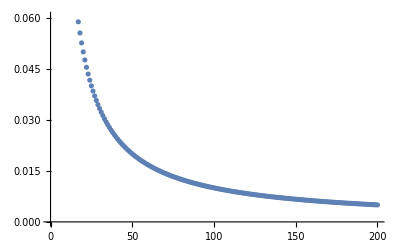

```mathematica
ListPlot[an]
```

```mathematica
P=Table[{i,k an[[i]]},{k,1,200},{i,1,100}];
```

```mathematica
epsilon=Table[1/n,{n,1,200}];
```

```mathematica
anm={};
am={};
bm={};
cm={};
```

```mathematica
a=1;
b=0.5;
c=1.5;
```

```mathematica
For[i=1,i<=100,i=i+1,
anm=Append[anm,
First[Select[an,# <epsilon[[i]]&]]
];
am=Append[am,{i,First[Select[Table[k anm[[i]],{k,200}],Abs[a-# ]<epsilon[[i]] &]]}]
];
am;
```

```mathematica
For[i=1,i<=100,i=i+1,
anm=Append[anm,
First[Select[an,# <epsilon[[i]]&]]
];
bm=Append[bm,{i,First[Select[Table[k anm[[i]],{k,200}],Abs[b-# ]<epsilon[[i]] &]]}]
];
bm;
```

```mathematica
For[i=1,i<=100,i=i+1,
anm=Append[anm,
First[Select[an,# <epsilon[[i]]&]]
];
cm=Append[cm,{i,First[Select[Table[k anm[[i]],{k,200}],Abs[c-# ]<epsilon[[i]] &]]}]
];
cm;
```

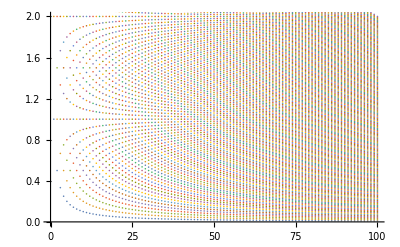

```mathematica
imagea=ListPlot[P,PlotRange->{All,{0,2}}]
```

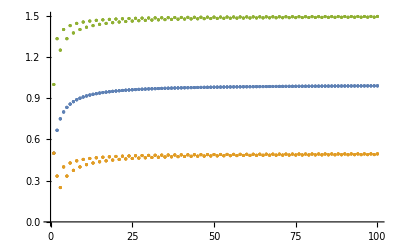

```mathematica
imageb=ListPlot[{am,bm,cm},PlotStyle->Thickness[0.01]]
```

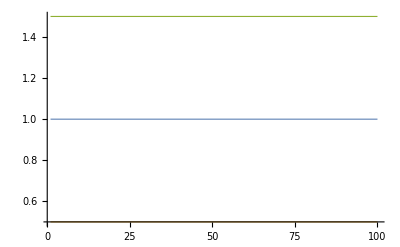

```mathematica
imagec=Plot[{a+0x,b+0 x,c+0 x},{x,1,100},PlotStyle->Thickness[0.002]]
```

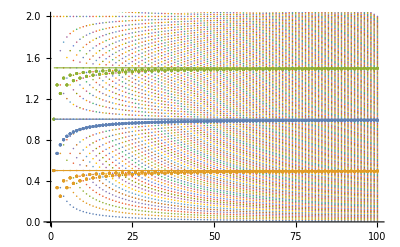

```mathematica
Show[imagea,imageb,imagec]
```